```mathematica
f[x_]=1/(2*x^2+3)^(1/2);
```

```mathematica
x=Table[i,{i,0.8,1.2,0.2}];
```

```mathematica
y=Table[N[f[i]],{i,0.8,1.2,0.2}];
```

```mathematica
xy=Table[{x[[i]],y[[i]]},{i,1,3}]
```

{{0.8,0.483368},{1.,0.447214},{1.2,0.412393}}

```mathematica
der1f1 = (xy[[2]][[2]]-xy[[1]][[2]])/0.2
```

-0.180773

```mathematica
der1f3 =( xy[[1]][[2]]-4*xy[[2]][[2]]+3*xy[[3]][[2]])/0.4
```

-0.170767

```mathematica
der1f2 = (xy[[3]][[2]]-xy[[1]][[2]])/0.4
```

-0.177438

```mathematica
Clear[x]
```

```mathematica
derf = D[f[x],x]
```

-(2 x)/((3+2 x^2)^(3/2))

```mathematica
x = 0.8;
```

```mathematica
derf
```

-0.180698

```mathematica
Abs[der1f1-derf]
```

0.0124496

```mathematica
x=1;
```

```mathematica
N[derf]
```

-0.178885

```mathematica
Abs[der1f2-derf]
```

0.00911429

```mathematica
x=1.2;
```

```mathematica
N[derf]
```

```mathematica
Abs[der1f3-derf]
```

0.00244378

```mathematica
der2 = (-f[1.2]+16*f[1.1]-30*f[1.0]+16*f[0.9]-f[0.8])/(12*0.1^2)
```

0.035775

```mathematica
Clear[x]
```

```mathematica
derf2 = D[-(2 x)/((3+2 x^2)^(3/2)), x]
```

(12 x^2)/((3+2 x^2)^(5/2))-2/((3+2 x^2)^(3/2))

```mathematica
x=1.0;
```

```mathematica
derf2
```

0.0357771

```mathematica
Abs[der2-derf2]
```

0.0300659

```mathematica
Clear[x]
```

```mathematica
pol = Expand[InterpolatingPolynomial[xy, x]]
```

0.641328-0.210791 x+0.0166763 x^2

```mathematica
derpol1 =D[pol,x]
```

-0.210791+0.0333526 x

```mathematica
x = 0.8;
```

```mathematica
derpol1
```

-0.184109

```mathematica
x = 1.0;
```

```mathematica
derpol1
```

-0.177438

```mathematica
x=1.2;
```

```mathematica
derpol1
```

-0.170767

```mathematica
Clear[x]
```

```mathematica
D[f[x],x]
```

-(2 x)/((3+2 x^2)^(3/2))

```mathematica
D[-(2 x)/((3+2 x^2)^(3/2)),x]
```

(12 x^2)/((3+2 x^2)^(5/2))-2/((3+2 x^2)^(3/2))

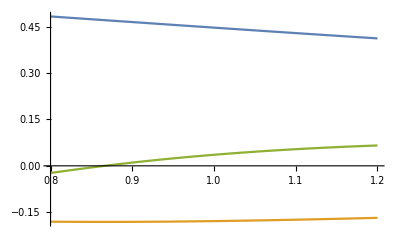

```mathematica
Show[Plot[{f[x],-(2 x)/((3+2 x^2)^(3/2)), (12 x^2)/((3+2 x^2)^(5/2))-2/((3+2 x^2)^(3/2))}, {x, 0.8,1.2}]]
```

```mathematica
a = 0.8; b= 1.2; h = 0.05;
```

```mathematica
n = Ceiling[(b-a)/h]
```

8

```mathematica
J = N[h/2*(f[a]+2*Sum[f[a+h*j], {j, 1,n-1}]+f[b])]
```

0.17898

```mathematica
Intg =Integrate[f[x], {x,a,b}]
```

0.178977

```mathematica
Abs[J - Intg]
```

2.58055×10^-6

```mathematica
maxder = FindMaximum[D[f[x],x], {x, 0.8, 1.2}][[1]]
```

0.181444

```mathematica
Rx = (h^2*(b-a))/12*maxder
```

0.0000151203

```mathematica
h=h*2;
```

```mathematica
J1 = N[h/2*(f[a]+2*Sum[f[a+h*j], {j, 1,n-1}]+f[b])]
```

0.17898

```mathematica
delt = 1/3*Abs[J-J1]
```

0.

```mathematica
s = (2^2*J-J1)/(2^2-1)
```

0.17898

```mathematica
h=0.05/2;
```

```mathematica
n = Ceiling[(b-a)/h];
```

```mathematica
J2 = N[h/2*(f[a]+2*Sum[f[a+h*j], {j, 1,n-1}]+f[b])]
```

0.178978

```mathematica
s1=(2^2*J2-J)/(2^2-1)
```

0.178977

```mathematica
s2 = (2^2*s1-s)/(2^2-1)
```

0.178976

```mathematica
Abs[s2-s1]
```

8.60392×10^-7

```mathematica
M=7;
T[0]=0.5(b-a)*(f[a]+f[b]);
Do[h=(b-a)/(2^j);n=2^(j-1);
T[j]=0.5*T[j-1]+h*Sum[f[a+(2k-1)*h],{k,n}],{j,1,M-1}]
Array[T,M,0];
```

```mathematica
Delta = Abs[T[M-1]-J]/J
```

0.0000141931